## Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Set Current Working Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\Desktop"];
```

## Load Insertion Device Functions

Open and evaluate the notebook “IDFunctions.nb”

## Usage Example

## Parameters

```mathematica
(*ID parameters*)
λu = 20; (*Period [mm]*)
Np = 3; (*Number of periods (not including terminations)*)
Br = 1.31; (*Remanent magnetization [T]*)
Gap = 6.5; (*Minimum ID gap [mm]*)
Termination = "None"; 

(*Longitudinal range [mm]*)
Lstep = 0.1;
Li = -(Np+2)*λu;
Lf = (Np+2)*λu;
Lnpts =Round[(Lf - Li)/Lstep ]+ 1; 

(*Horizontal range [mm]*)
Hstep =0.5;
Hi = -3;
Hf = 3;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1; 

(*Vertical range [mm]*)
Vstep =0.5;
Vi = -3;
Vf = 3;
Vnpts = Round[(Vf - Vi)/Vstep ]+ 1; 

(*Particle energy [GeV]*)
Energy = 3;

(*Radia randomization magnitudes*)
radFldLenTol[10^-12,10^-12 ];
```

## Model

IDDelta: elapsed time = 0.156276 s

-Graphics3D-

IDShow: elapsed time = 0.4374912 s

-Graphics3D-

IDShow: elapsed time = 0.187505 s

IDPlotFields: elapsed time = 2.828115 s

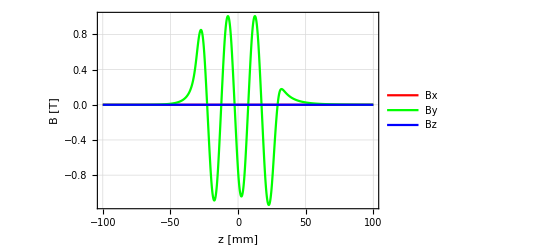

```mathematica
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockVersion"-> "Prototype"];
IDShow[Device]
IDShow[Device, "MagDirection"-> True, "ArrowSize"-> 5]
Show[IDPlotFields[Device, "z", {Li, Lf}], PlotRange-> All, FrameLabel-> {"z [mm]", "B [T]"}]
```

## Field Integrals

```mathematica
IDFieldIntegrals[Device, "by", {Li, Lf}, Lnpts];
```

First integral: -16.4818 G.cm

Second integral: 1.74748 T.cm.b2

IDFieldIntegrals: elapsed time = 3.453101 s

## Trajectory

IDRungeKuttaTrajectory: elapsed time = 3.7187086 s

IDPlotRungeKuttaTrajectory: elapsed time = 0.14065 s

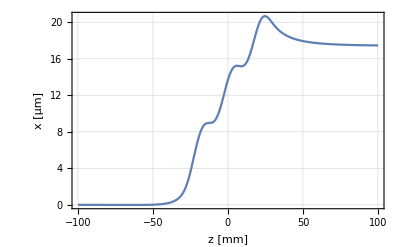
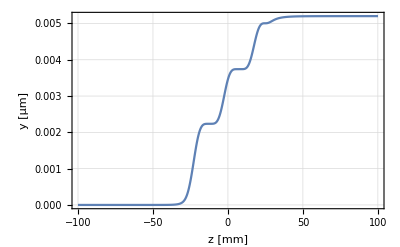

```mathematica
Trajectory = IDRungeKuttaTrajectory[Device, Energy, {0, 0, Li, 0, 0, 1}, Lf,Lstep ];
IDPlotRungeKuttaTrajectory[Trajectory]
```

## Field Map

```mathematica
FieldMapFilename = "device_fieldmap.txt";
IDFieldMap[FieldMapFilename, Device, {Hi, Hf}, {0, 0}, {Li, Lf}, Hnpts, 1, Lnpts];
```

Fieldmap saved in file: device_fieldmap.txt

IDFieldMapNoTransf: elapsed time = 14.017216 s